```mathematica
m[t_,z_]=1/2 + 1/4 Cos[π t/2] - z
uExact[t_,x_,y_]=Exp[-1/4(m[t,x]^2+m[t,y]^2)]
```

1/2-z+1/4 Cos[(π t)/2]

ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2))

```mathematica
f[t_,x_,y_]=D[uExact[t,x,y],t]-lambda Laplacian[uExact[t,x,y],{x,y}] + {bx,by}.Grad[uExact[t,x,y],{x,y}]
```

-lambda (-ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2))+1/4 ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2)) (1/2-x+1/4 Cos[(π t)/2])^2+1/4 ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2)) (1/2-y+1/4 Cos[(π t)/2])^2)+1/2 bx ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2)) (1/2-x+1/4 Cos[(π t)/2])+1/2 by ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2)) (1/2-y+1/4 Cos[(π t)/2])+1/4 ⅇ^(1/4 (-(1/2-x+1/4 Cos[(π t)/2])^2-(1/2-y+1/4 Cos[(π t)/2])^2)) (1/4 π (1/2-x+1/4 Cos[(π t)/2]) Sin[(π t)/2]+1/4 π (1/2-y+1/4 Cos[(π t)/2]) Sin[(π t)/2])

```mathematica
CForm[f[t,x,y]]
```

-(lambda*(-Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
             Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.) + 
        (Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
               Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)*
           Power(0.5 - x + Cos((Pi*t)/2.)/4.,2))/4. + 
        (Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
               Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)*
           Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)) + 
   (bx*Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
          Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)*
      (0.5 - x + Cos((Pi*t)/2.)/4.))/2. + 
   (by*Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
          Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)*
      (0.5 - y + Cos((Pi*t)/2.)/4.))/2. + 
   (Power(E,(-Power(0.5 - x + Cos((Pi*t)/2.)/4.,2) - 
          Power(0.5 - y + Cos((Pi*t)/2.)/4.,2))/4.)*
      ((Pi*(0.5 - x + Cos((Pi*t)/2.)/4.)*Sin((Pi*t)/2.))/4. + 
        (Pi*(0.5 - y + Cos((Pi*t)/2.)/4.)*Sin((Pi*t)/2.))/4.))/4.

```mathematica
Animate[ContourPlot[uExact[t,x,y],{x,0,1},{y,0,1},PlotLegends->Automatic,PlotPoints->25],{t,0,2}]
```

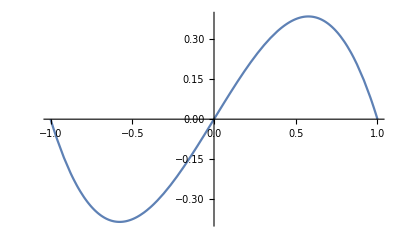

```mathematica
Plot[x-x^3,{x,-1,1}]
```